```mathematica
a=6.0675;
c=3.6570;
primvecs={a{1,0,0},a{-1/2,(√3)/2,0},c{0,0,1}};
reciprocalVectors[primitiveVectors_]:=
(
a1=primitiveVectors[[1]];
a2=primitiveVectors[[2]];
a3=primitiveVectors[[3]];
2π{Cross[a2,a3]/(a1.Cross[a2,a3]),Cross[a3,a1]/(a2.Cross[a3,a1]),Cross[a1,a2]/(a3.Cross[a1,a2])}
)
recVectors=reciprocalVectors@primvecs;

kvec[kx_,ky_,kz_]:={kx,ky,kz};

tz=1;

tPerp=3;
tzp=2;
t2p=1.5;

hamiltonian[kx_,ky_,kz_]:=-tz{{0,ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]])),ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[1]])},{ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]])),0,ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[2]])},{ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[1]]),ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[2]]),0}};

hamiltonian2[kx_,ky_,kz_]:=-{{0,tPerp,tPerp,tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])},{tPerp,0,tPerp,t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])},{tPerp,tPerp,0,t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])},
{tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),0,tPerp,tPerp},{t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),tPerp,0,tPerp},{t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),tPerp,tPerp,0}};

hamiltonian3[kx_,ky_,kz_]:=-{{0,tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[1]]),tPerp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[2]]),tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]+primvecs[[3]])),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[2]]+primvecs[[3]]))},{tPerp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[1]]),0,tPerp ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]])),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[3]])),tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]]))},{tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[2]]),tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]])),0,t2p ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[2]]+primvecs[[3]])),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]-primvecs[[2]]+primvecs[[3]])),tzp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])},
{tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[3]])),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[2]]-primvecs[[3]])),0,tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[1]]),tPerp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[2]])},{t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]-primvecs[[3]])),tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),t2p ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]-primvecs[[3]])),tPerp ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[1]]),0,tPerp ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]))},{t2p ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[2]]+primvecs[[3]])),t2p ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]])),tzp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[3]]),tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[2]]),tPerp ⅇ^(-ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]])),0}};

point1=.5recVectors[[1]];
point2={.25Norm@recVectors[[1]],.5Norm@recVectors[[1]],0};
nPoints=100;

kPath[t_]:=Piecewise[{{point1 t,0≤ t≤ 1},{(point2-point1) (t-1)+point1,1≤ t≤ 2},{(origin-point2) (t-2)+(point2),2≤ t≤ 3},{π/(2c){0,0,1}(t-3),3≤ t≤ 4},{point1 (t-4)+π/(2c){0,0,1},4≤ t≤ 5},{(point2-point1) (t-5)+point1+π/(2c){0,0,1},5≤ t≤ 6},{(origin-point2) (t-6)+(point2)+π/(2c){0,0,1},6≤ t≤ 7}}]
kPoints=kPath[#]&/@Range[0,7,1/nPoints];


hamiltonians=hamiltonian[kPoints[[#,1]],kPoints[[#,2]],kPoints[[#,3]]]&/@Range@Length@kPoints;
hamiltonians2=hamiltonian2[kPoints[[#,1]],kPoints[[#,2]],kPoints[[#,3]]]&/@Range@Length@kPoints;
hamiltonians3=hamiltonian3[kPoints[[#,1]],kPoints[[#,2]],kPoints[[#,3]]]&/@Range@Length@kPoints;
eigs=Sort/@Chop@Eigenvalues/@hamiltonians;
eigs2=Sort/@Chop@Eigenvalues/@hamiltonians2;
eigs3=Sort/@Chop@Eigenvalues/@hamiltonians3;

g1=ListPlot[Transpose@eigs,Joined->True];
g2=ListPlot[Transpose@eigs2,Joined->True];
g3=ListPlot[Transpose@eigs3,Joined->True];
```

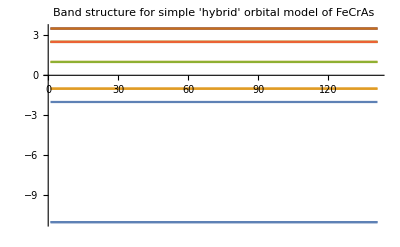

```mathematica
Show[g1,g2,g3,PlotRange->All,PlotLabel-> "Band structure for simple 'hybrid' orbital model of FeCrAs"]
```

```mathematica
errorsOff[]:=(Off[NIntegrate::slwcon];
Off[NIntegrate::eincr];
Off[NIntegrate::oidiv];)
errorsOff[]

a0=1;
ρ[n_,r_]:=(2 r)/(n a0);
ψnlm[n_,l_,m_,r_,θ_,ϕ_]:=Sqrt[(2/(n a0))^3 (n-l-1)!/(2 n (n+l)!)]
E^(-ρ[n,r]/2) ρ[n,r]^l LaguerreL[n-l-1,2 l+1,ρ[n,r]] SphericalHarmonicY[l,m,θ,ϕ]
ψnlmCart[n_,l_,m_,x_,y_,z_]:=Sqrt[(2/(n a0))^3 (n-l-1)!/(2 n (n+l)!)]
E^(-ρ[n,r]/2) ρ[n,r]^l LaguerreL[n-l-1,2 l+1,ρ[n,r]] SphericalHarmonicY[l,m,θ,ϕ]/.{r->Sqrt[x^2+y^2+z^2],θ->ArcCos[z/Sqrt[x^2+y^2+z^2]],ϕ->ArcCos[x/Sqrt[x^2+y^2]]}

R1[r_]:=2/a0^(3/2) E^(-r/a0)
R2[r_]:=r/a0 E^(-r/(2 a0))
ψx[x_,y_,z_]:=R2[r] x/r/.r->Sqrt[x^2+y^2+z^2]
Nx=1/(√NIntegrate[ψx[x,y,z]* ψx[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψxNorm[x_,y_,z_]:=Nx ψx[x,y,z]
ψy[x_,y_,z_]:=R2[r] y/r/.r->Sqrt[x^2+y^2+z^2]
Ny=1/(√NIntegrate[ψy[x,y,z]* ψy[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψyNorm[x_,y_,z_]:=Ny ψy[x,y,z]
ψz[x_,y_,z_]:=R2[r] z/r/.r->Abs[Sqrt[x^2+y^2+z^2]]
Nz=1/(√NIntegrate[ψz[x,y,z]* ψz[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψzNorm[x_,y_,z_]:=Nz ψz[x,y,z]
porbs[x_,y_,z_]:={ψxNorm[x,y,z],ψyNorm[x,y,z],ψzNorm[x,y,z]}


(*Definition of the 1s wavefunction*)
ψ4sNorm[x_,y_,z_]:=ψnlm[1,0,0,r,θ,ϕ]/.r->Sqrt[x^2+y^2+z^2]

(*Definition of the 3d wavefunctions*)

R32[r_]:=r^2 E^(-r/(3 a0));
ψxy[x_,y_,z_]:=(x y)/r^2 R32[r]/.r->Sqrt[x^2+y^2+z^2]
Nxy=1/(√NIntegrate[ψxy[x,y,z]* ψxy[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψxyNorm[x_,y_,z_]:=Nxy ψxy[x,y,z]
ψxz[x_,y_,z_]:=(x z)/r^2 R32[r]/.r->Sqrt[x^2+y^2+z^2]
Nxz=1/(√NIntegrate[ψxz[x,y,z]* ψxz[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψxzNorm[x_,y_,z_]:=Nxz ψxz[x,y,z]
ψyz[x_,y_,z_]:=(y z)/r^2 R32[r]/.r->Sqrt[x^2+y^2+z^2]
Nyz=1/(√NIntegrate[ψyz[x,y,z]* ψyz[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψyzNorm[x_,y_,z_]:=Nyz ψyz[x,y,z]
ψz2[x_,y_,z_]:=(3 z^2-r^2)/r^2 R32[r]/.r->Sqrt[x^2+y^2+z^2]
Nz2=1/(√NIntegrate[ψz2[x,y,z]* ψz2[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψz2Norm[x_,y_,z_]:=Nz2 ψz2[x,y,z]
ψx2y2[x_,y_,z_]:=(x^2-y^2)/r^2 R32[r]/.r->Sqrt[x^2+y^2+z^2]
Nx2y2=1/(√NIntegrate[ψx2y2[x,y,z]* ψx2y2[x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞}]);
ψx2y2Norm[x_,y_,z_]:=Nx2y2 ψx2y2[x,y,z]

ψCentral[x_,y_,z_]:={ψ4sNorm[x,y,z],ψxyNorm[x,y,z],ψxzNorm[x,y,z],ψyzNorm[x,y,z],ψz2Norm[x,y,z],ψx2y2Norm[x,y,z]}
pyrState[x_,y_,z_]:=ψCentral[x,y,z][[2;;6]];
pyrStateb[rho_,theta_,phi_]:=pyrState[x,y,z]/.{x->rho Sin[theta] Cos[phi],y->rho Sin[theta] Sin[phi],z->rho Cos[theta]}
x1[rho_,theta_,phi_]:=rho*Sin[theta]*Cos[phi]
y1[rho_,theta_,phi_]:=rho*Sin[theta]*Sin[phi]
z1[rho_,theta_,phi_]:=rho*Cos[theta]
(*Pyramid vertices*)

P[rho_,theta_,phi_]:={x1[rho,theta,phi],y1[rho,theta,phi],z1[rho,theta,phi]};
pyr={{2.51559,0.,0.},{-0.518164,-1.75154,-1.8285},{-0.518164,-1.75154,1.8285},{-0.518164,1.75154,-1.8285},{-0.518164,1.75154,1.8285}};
t=0.2;
H1[rho_,theta_,phi_]:=Sum[(1/Sqrt[((Norm[P[rho,theta,phi]-pyr[[i]]]))^2+t^2]),{i,1,Length@pyr}]
range=∞;
V1[i_,j_]:=NIntegrate[pyrStateb[rho,theta,phi][[i]]*H1[rho,theta,phi]*pyrStateb[rho,theta,phi][[j]] rho^2 Sin[theta],{rho,0,range},{theta,0,π},{phi,0,2 π}]
```

2^l ⅇ^(-r/n) (r/n)^l LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,ϕ]

2^l ⅇ^(-(√(x^2+y^2+z^2))/n) ((√(x^2+y^2+z^2))/n)^l LaguerreL[-1-l+n,1+2 l,(2 √(x^2+y^2+z^2))/n] SphericalHarmonicY[l,m,ArcCos[z/(√(x^2+y^2+z^2))],ArcCos[x/(√(x^2+y^2))]]

```mathematica
HCF=Monitor[Table[V1[i,j],{i,5},{j,5}],{i,j}]
```

```mathematica
Clear@t
```

```mathematica
pyrData=<<"~/Documents/pyramid/changesArray_pyramid.txt";
eigs=Chop@Eigensystem@HCF;
CFS𝒰=eigs[[2]];
pyr𝒰=construct𝒰tot[IdentityMatrix[5],pyrData];
```

```mathematica
hamiltonianFinal[kx_,ky_,kz_]:=ArrayFlatten[{{hamiltonian2[kx,ky,kz],ConstantArray[0,{6,6}],ConstantArray[0,{6,3}]},{ConstantArray[0,{6,6}],hamiltonian3[kx,ky,kz],ConstantArray[0,{6,3}]},
{ConstantArray[0,{3,6}],ConstantArray[0,{3,6}],hamiltonian[kx,ky,kz]}}]+ArrayFlatten[Table[IdentityMatrix[3]newMat2[[i,j]],{i,5},{j,5}]]
hamiltoniansFinal=hamiltonianFinal[kPoints[[#,1]],kPoints[[#,2]],kPoints[[#,3]]]&/@Range@Length@kPoints;
eigsFinal=Sort/@Chop@Eigenvalues/@hamiltoniansFinal;
finalPlot=ListPlot[Transpose@eigsFinal,Joined->True,PlotRange->All,PlotLabel->"Band Structure for Cr-Cr Hopping Model with Crystal Field Splitting",AxesLabel->{"","Energy(eV)"},Ticks->{{{0,"Γ"},{nPoints,"M"},{2nPoints,"K"},{3nPoints,"Γ"},{4nPoints,"A"},{5nPoints,"L"},{6nPoints,"H"},{7nPoints,"A"}},All}];
Export["~/Documents/bandStructure3.pdf",finalPlot]
```

~/Documents/bandStructure3.pdf

## Fe-Fe block of the Hamiltonian

```mathematica
hamiltonianFeFe[kx_,ky_,kz_]:={{ConstantArray[0,{3,3}],{{tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]-primvecs[[2]]+primvecs[[3]]))},{tzFep ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]-primvecs[[2]]+primvecs[[3]]))},{tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]])),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]])),tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])}},ConstantArray[0,{3,3}],ConstantArray[0,{3,3}]},{{{tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]-primvecs[[2]]+primvecs[[3]]))},{tzFep ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]]),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(-primvecs[[1]]-primvecs[[2]]+primvecs[[3]]))},{tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]])),tzFep ⅇ^(ⅈ kvec[kx,ky,kz].(primvecs[[1]]+primvecs[[2]]+primvecs[[3]])),tzFe ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[3]])}}†,ConstantArray[0,{3,3}],ConstantArray[0,{3,3}],ConstantArray[0,{3,3}]},{ConstantArray[0,{3,3}],ConstantArray[0,{3,3}],tperpFe{{ 0,ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[1]]),ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[1]])},{ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[1]]),0,1},{ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[1]]),1, 0}},ConstantArray[0,{3,3}]},{ConstantArray[0,{3,3}],ConstantArray[0,{3,3}],ConstantArray[0,{3,3}],tperpFe{{ 0,ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[2]]),1},{ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[2]]),0,ⅇ^(-ⅈ kvec[kx,ky,kz].primvecs[[2]])},{1,ⅇ^(ⅈ kvec[kx,ky,kz].primvecs[[2]]), 0}}}}
```